```mathematica
Clear["Global`*"]
```

{{{0.,-0.1}},{{0.,-0.095}},{{0.,-0.09}},{{0.,-0.085}},{{0.,-0.08}},{{0.,-0.075}},{{0.,-0.07}},{{0.,-0.065}},4125,{{1.,0.065}},{{1.,0.07}},{{1.,0.075}},{{1.,0.08}},{{1.,0.085}},{{1.,0.09}},{{1.,0.095}},{{1.,0.1}}}
 |  |  |  |

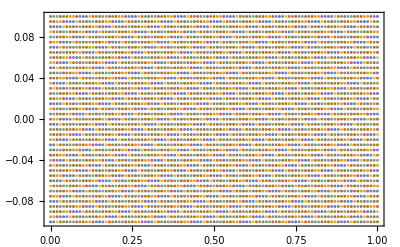

```mathematica
LISTA=Partition[Partition[Flatten[Table[{x,y},{x,0,1,0.01},{y,-0.1,0.1,0.005}]],2],1]
ListPlot[LISTA⟦All,All,1;;2⟧,Frame->True]
```

```mathematica
Length[LISTA]
```

4141

```mathematica
LISTA;
```

```mathematica
DLISTA=Map[Directive,Partition[Flatten[Table[{Hue[x],PointSize[y+0.11],Opacity[0.01]},{x,0,1,0.01},{y,-0.1,0.1,0.005}]],3]];
```

```mathematica
Length[DLISTA]
```

4141

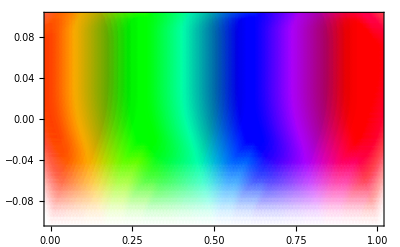

```mathematica
ListPlot[LISTA⟦All,All,1;;2⟧,PlotStyle->DLISTA,Frame->True]
```

```mathematica
imag=(y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7);
real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

{{{6.80024,1.29799}},{{6.35359,0.687699}},{{5.88751,0.153035}},{{5.40842,-0.307816}},4134,{{5.88751,0.153035}},{{6.35359,0.687699}},{{6.80024,1.29799}}}
 |  |  |  |

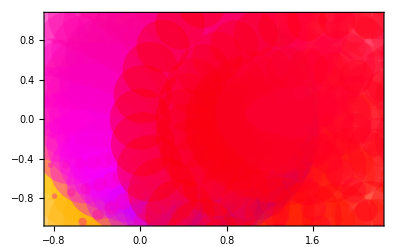

```mathematica
MAPLISTA=Block[{μ= 3.7},Partition[Partition[Flatten[Table[{real,imag},{x,0,1,0.01},{y,-0.1,0.1,0.005}]],2],1]]
ListPlot[MAPLISTA⟦All,All,1;;2⟧,Frame->True,PlotStyle->DLISTA]
```

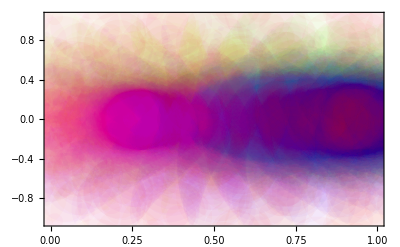

```mathematica
ListPlot[MAPLISTA⟦All,All,1;;2⟧,Frame->True,PlotStyle->DLISTA,PlotRange->{{0,1},Automatic}]
```